# Single traj

```mathematica
importTraj[dir_,sample_]:=Module[
{data,fname}
,
SetDirectory[dir];
fname=IntegerString[sample,10,3]<>".txt";
If[!FileExistsQ[fname],
fname=IntegerString[sample,10,4]<>".txt"
];
data=Import[fname,"Table"];
data=Transpose[{data[[2;;,1]],data[[2;;,3]]}];
Return[data];
]
```

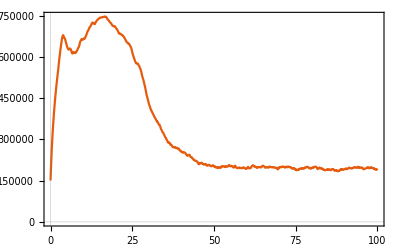

```mathematica
sample=20;

dir=NotebookDirectory[]<>"../data_tau_leaping/vol_exp_12/ip3r_01000/ip3_1p700/";
data=importTraj[dir,sample];
ListLinePlot[data]
```

# Single traj: compare gillespie & tau leaping

```mathematica
importTrajLegacy[dir_,sample_]:=Module[
{data}
,
SetDirectory[dir];
data=Import[IntegerString[sample,10,3]<>"/ca2i.txt","Table"];
Return[data];
]
```

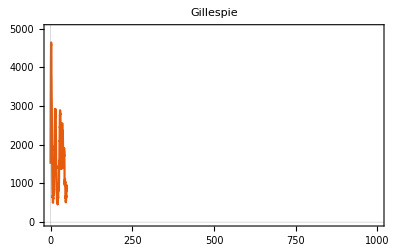

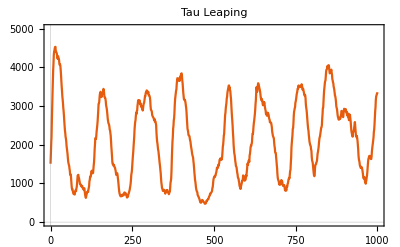

```mathematica
sample=50;

dir=NotebookDirectory[]<>"../data_gillespie_rw/vol_exp_14/ip3r_00200/ip3_0p500/";
data=importTraj[dir,sample];
ListLinePlot[data,PlotRange->{{0,1000},{0,5000}},PlotLabel->"Gillespie"]

dir=NotebookDirectory[]<>"../data_tau_leaping_rw/vol_exp_14/ip3r_00200/ip3_0p500/";
data=importTraj[dir,sample];
ListLinePlot[data,PlotRange->{{0,1000},{0,5000}},PlotLabel->"Tau Leaping"]
```

# Different IP3R

```mathematica
sampleStart=0;
sampleEnd=99;
noIP3Rs={100,200,300,400,500,600,700,800,900,1000,5000};
ip3="ip3_0p800";

data=Association[];
mean=Association[];
std=Association[];

Monitor[
Do[
noIP3R=noIP3Rs[[i]];

data[noIP3R]={};
If[noIP3R≠5000,
dir=NotebookDirectory[]<>"../data_gillespie_rw/vol_exp_14/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/",
dir=NotebookDirectory[]<>"../data_tau_leaping_rw/vol_exp_14/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/"
];

Do[
AppendTo[data[noIP3R],importTraj[dir,sample][[;;500]]];
,{sample,sampleStart,sampleEnd}];

t=data[noIP3R][[1,;;,1]];
mean[noIP3R]=Transpose[{t,Mean[data[noIP3R][[;;,;;,2]]]}]//N;
std[noIP3R]=Transpose[{t,StandardDeviation[data[noIP3R][[;;,;;,2]]]}]//N;
,{i,Length[noIP3Rs]}];
,ProgressIndicator[i,{1,Length[noIP3Rs]}]]
```

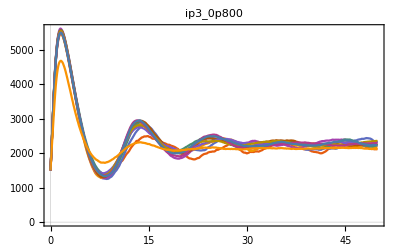
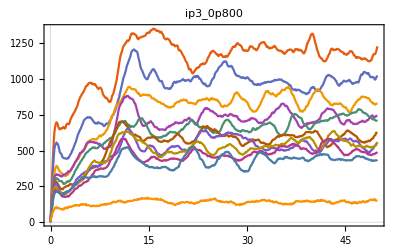

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

leg=LineLegend[colors[[;;Length[noIP3Rs]]],Keys[data]];

Row[{
ListLinePlot[Values[mean],PlotRange->All,PlotLabel->ip3],
ListLinePlot[Values[std],PlotRange->All,PlotLabel->ip3],
leg
}]
```

```mathematica
sampleStart=0;
sampleEnd=99;
noIP3Rs={500,1000,2000};
ip3="ip3_0p300";

data=Association[];
mean=Association[];
std=Association[];

Monitor[
Do[
noIP3R=noIP3Rs[[i]];

data[noIP3R]={};
If[noIP3R≠2000&&noIP3R≠1000,
dir=NotebookDirectory[]<>"../data_gillespie/vol_exp_14/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/",
dir=NotebookDirectory[]<>"../data_tau_leaping/vol_exp_14/ip3r_"<>IntegerString[noIP3R,10,5]<>"/"<>ip3<>"/"
];

Do[
AppendTo[data[noIP3R],importTraj[dir,sample][[;;500]]];
,{sample,sampleStart,sampleEnd}];

t=data[noIP3R][[1,;;,1]];
mean[noIP3R]=Transpose[{t,Mean[data[noIP3R][[;;,;;,2]]]}]//N;
std[noIP3R]=Transpose[{t,StandardDeviation[data[noIP3R][[;;,;;,2]]]}]//N;
,{i,Length[noIP3Rs]}];
,ProgressIndicator[i,{1,Length[noIP3Rs]}]]
```

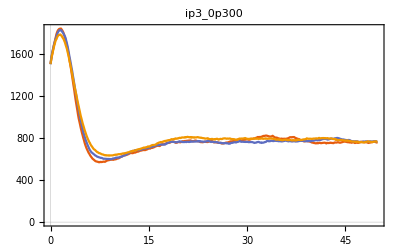
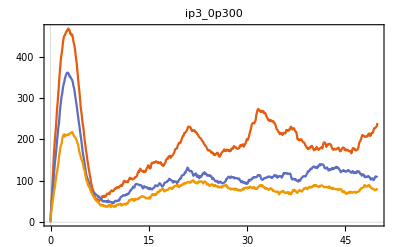

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

leg=LineLegend[colors[[;;Length[noIP3Rs]]],Keys[data]];

Row[{
ListLinePlot[Values[mean],PlotRange->All,PlotLabel->ip3],
ListLinePlot[Values[std],PlotRange->All,PlotLabel->ip3],
leg
}]
```